| Estimate | Standard Error | t-Statistic | P-Value
a | -0.211885 | 0.0259007 | -8.18065 | 2.91786×10^-8
b | 9.26019 | 0.0557793 | 166.015 | 6.43935×10^-37
Ref | 7.29879 | 0.0872732 | 83.6315 | 4.42565×10^-30

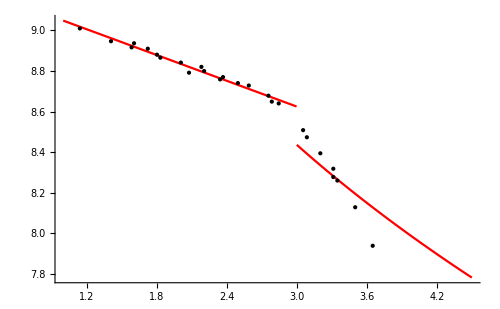

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["noyola_ready_0,25.dat"];
L=Length[data];
Ie=1000;
Ip[R_]:=Piecewise[{{a*R+b,R<3},{Log[Ie*Exp[-7.669*((R/Ref)^0.25-1.0)]],R>3}}]
(*Plot[Log[Ip[R]],{R,0,12}]*)
fit = NonlinearModelFit[data,Ip[R],{a,b,Ref},R,MaxIterations->1000];
(*fit//Normal//InputForm*)
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,1,4.5},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```